## Tunneling through a fluctuating barrier: Two-level model

### Informal supplementary Mathematica.NB "https://journals.aps.org/pre/abstract/10.1103/PhysRevE.61.4890"

```mathematica
SapiroLoginov[{κ_,ϵ_,Δ0_,Δ1_,ν_},initC_,tf_]:=Block[{A,R,t,init,out},
A={
{-2 κ,-ϵ,0,0,0,0},
{ϵ,-2κ,Δ0,0,0,Δ1},
{0,-Δ0,0,0,-Δ1,0},
{0,0,0,-2 κ-2ν,-ϵ,0},
{0,0,Δ1,ϵ,-2 κ-2ν,Δ0},
{0,-Δ1,0,0,-Δ0,-2ν}
};
init=PadRight[initC,6];
NDSolveValue[{R'[t]==A.R[t],R[0]==init},R,{t,0,tf}]
];
(*eq 3 (a.b.c)*)
(*{κ_,ϵ_,Δ0_,Δ1_,ν_}
list of paramter*)
(*initC_
list of numbers of same 3b automatic are zero Padding to right *)
```

```mathematica
(*genetat fig for 4 parameter*)
plotFig4[Δ1_,ϵ_]:=Block[{Δ0=1,ν=0,
κ,sol,p,pl1,pl2,pl3,pl4},

(*----------------------------------------*)
κ=.01;
sol=SapiroLoginov[{κ,ϵ,Δ0,Δ1,ν},{0,0,1},80];
p[t_]:=.5(sol[t][[3]]+1);
pl1=Plot[p[t],{t,0,80},PlotRange->{0,1},PlotStyle->{Dotted,Black}];
(*----------------------------------------*)
κ=.1;
sol=SapiroLoginov[{κ,ϵ,Δ0,Δ1,ν},{0,0,1},80];
p[t_]:=.5(sol[t][[3]]+1);
pl2=Plot[p[t],{t,0,80},PlotRange->{0,1},PlotStyle->{Black}];
(*----------------------------------------*)
κ=1;
sol=SapiroLoginov[{κ,ϵ,Δ0,Δ1,ν},{0,0,1},80];
p[t_]:=.5(sol[t][[3]]+1);
pl3=Plot[p[t],{t,0,80},PlotRange->{0,1},PlotStyle->{DotDashed,Black}];
(*----------------------------------------*)
κ=100;
sol=SapiroLoginov[{κ,ϵ,Δ0,Δ1,ν},{0,0,1},80];
p[t_]:=.5(sol[t][[3]]+1);
pl4=Plot[p[t],{t,0,80},PlotRange->{0,1},PlotStyle->{DotDashed,Black}];
(*----------------------------------------*)
Show[pl1,pl2,pl3,pl4]]
```

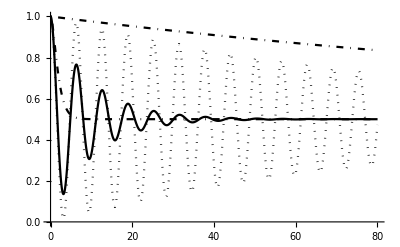

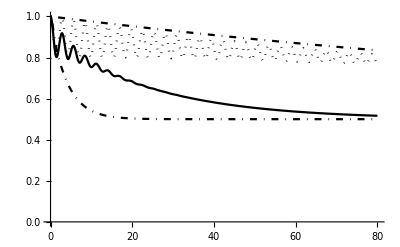

```mathematica
(*fig 1 a*)
Δ1=0;ϵ=0;
plotFig4[Δ1,ϵ]
(*fig 1 b*)
Δ1=0;ϵ=2;
plotFig4[Δ1,ϵ]
```

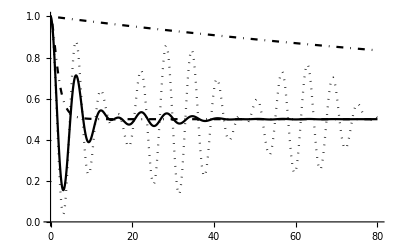

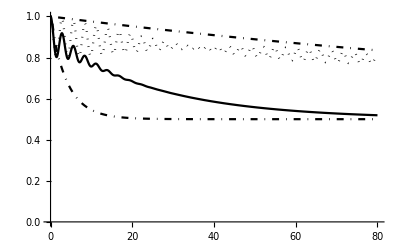

```mathematica
(*fig 2 a*)
Δ1=.1;ϵ=0;
plotFig4[Δ1,ϵ]
(*fig 2 b*)
Δ1=.1;ϵ=2;
plotFig4[Δ1,ϵ]
```

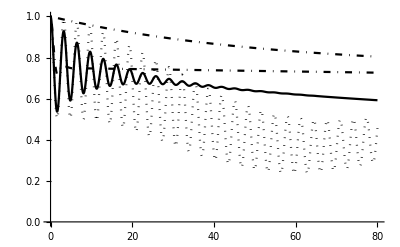

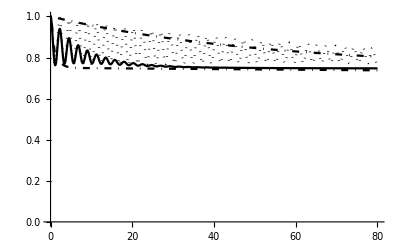

```mathematica
(*fig 1 a*)
Δ1=.95;ϵ=0;
plotFig4[Δ1,ϵ]
(*fig 1 b*)
Δ1=.95;ϵ=2;
plotFig4[Δ1,ϵ]
```